## Definitions

```mathematica
ClearAll["Global`*"]
```

## Common definitions

```mathematica
zeros=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});gmu=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});gm1=({{0, 0, 0, -I}, {0, 0, -I, 0}, {0, I, 0, 0}, {I, 0, 0, 0}});gm2=({{0, 0, 0, -1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {-1, 0, 0, 0}});gm3=({{0, 0, -I, 0}, {0, 0, 0, I}, {I, 0, 0, 0}, {0, -I, 0, 0}});gm4=({{0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}});gm5=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
gammalst={gm1,gm2,gm3,gm4,gm5};

(*
进行m从0到4n-1循环的时候用到，将m分成0-n之间的数和0-3之间的数两部分。
前者代表site，后者代表spinor index，又或者代表link
*)
spinnorsplit[n_]:=Return[{IntegerPart[n/4],Mod[n,4]}];

(*
L是格子宽度，
将site index，变成4维坐标。
注意，坐标原点(0,0,0,0)在角上。
*)
functionGetCoordinate[x_,l_]:={
IntegerPart[x/(l[[2]]*l[[3]]*l[[4]])],
Mod[IntegerPart[x/(l[[3]]*l[[4]])],l[[2]]],
Mod[IntegerPart[x/l[[4]]],l[[3]]],
Mod[x,l[[4]]]
};

(*
4维体积
*)
nall[L_]:=L[[1]]*L[[2]]*L[[3]]*L[[4]];

torusBound[x_,L_]:=Block[{retx},
retx=x;
If[retx[[1]]<0,retx[[1]]=retx[[1]]+L[[1]]];If[retx[[1]]>=L[[1]],retx[[1]]=retx[[1]]-L[[1]]];
If[retx[[2]]<0,retx[[2]]=retx[[2]]+L[[2]]];If[retx[[2]]>=L[[2]],retx[[2]]=retx[[2]]-L[[2]]];
If[retx[[3]]<0,retx[[3]]=retx[[3]]+L[[3]]];If[retx[[3]]>=L[[3]],retx[[3]]=retx[[3]]-L[[3]]];
If[retx[[4]]<0,retx[[4]]=retx[[4]]+L[[4]]];If[retx[[4]]>=L[[4]],retx[[4]]=retx[[4]]-L[[4]]];
Return[retx];
];

(* If torusOrDirichlet[[1]] is 0, it is Dirichlet, if it is 1, it is torus *)
dirichlet[x_,L_,torusOrDirichlet_]:=Block[{retx},
retx=x;
If[retx[[1]]<0,retx[[1]]=retx[[1]]+L[[1]]*torusOrDirichlet[[1]]];If[retx[[1]]>=L[[1]],retx[[1]]=retx[[1]]-L[[1]]*torusOrDirichlet[[1]]];
If[retx[[2]]<0,retx[[2]]=retx[[2]]+L[[2]]*torusOrDirichlet[[2]]];If[retx[[2]]>=L[[2]],retx[[2]]=retx[[2]]-L[[2]]*torusOrDirichlet[[2]]];
If[retx[[3]]<0,retx[[3]]=retx[[3]]+L[[3]]*torusOrDirichlet[[3]]];If[retx[[3]]>=L[[3]],retx[[3]]=retx[[3]]-L[[3]]*torusOrDirichlet[[3]]];
If[retx[[4]]<0,retx[[4]]=retx[[4]]+L[[4]]*torusOrDirichlet[[4]]];If[retx[[4]]>=L[[4]],retx[[4]]=retx[[4]]-L[[4]]*torusOrDirichlet[[4]]];
Return[retx];
];

projectiveXY[x_,L_]:=Block[{retx},
retx=x;
If[retx[[1]]<0,retx[[1]]=retx[[1]]+L[[1]];retx[[2]]=L[[2]]-retx[[2]]-1];If[retx[[1]]>=L[[1]],retx[[1]]=retx[[1]]-L[[1]];retx[[2]]=L[[2]]-retx[[2]]-1];
If[retx[[2]]<0,retx[[2]]=retx[[2]]+L[[2]];retx[[1]]=L[[1]]-retx[[1]]-1];If[retx[[2]]>=L[[2]],retx[[2]]=retx[[2]]-L[[2]];retx[[1]]=L[[1]]-retx[[1]]-1];
If[retx[[3]]<0,retx[[3]]=retx[[3]]+L[[3]]];If[retx[[3]]>=L[[3]],retx[[3]]=retx[[3]]-L[[3]]];
If[retx[[4]]<0,retx[[4]]=retx[[4]]+L[[4]]];If[retx[[4]]>=L[[4]],retx[[4]]=retx[[4]]-L[[4]]];
Return[retx];
];

(*
返回：{x+offset与y是否是同一个点， x到x+offset是否跨越t边界}
*)
isOffset[x_,y_,offsetv_,L_,boundary_]:=Block[{x1,x2,dx1,dx2},
x1=functionGetCoordinate[x,L];
x2=functionGetCoordinate[y,L];
dx1=x1+offsetv;
dx2=boundary[dx1,L];
Return[{dx2[[1]]==x2[[1]]&&dx2[[2]]==x2[[2]]&&dx2[[3]]==x2[[3]]&&dx2[[4]]==x2[[4]],dx1[[4]]!=dx2[[4]]}];
(*Return[{dx2[[1]]==x2[[1]]&&dx2[[2]]==x2[[2]]&&dx2[[3]]==x2[[3]]&&dx2[[4]]==x2[[4]],False}];*)
];

eta[n_,mu_]:=Product[(-1)^n[[nu]],{nu,1,mu-1}];

(*
mtr是gamma矩阵。

*)
diagnalTerm[coef_,L_,mtr_]:=Block[
{n1,n2,n1p,n2p},
Return[
coef Table[
n1=spinnorsplit[x];
n2=spinnorsplit[y];
n1p=functionGetCoordinate[n1[[1]],L];
n2p=functionGetCoordinate[n2[[1]],L];
If[n1p[[1]]==n2p[[1]]&&n1p[[2]]==n2p[[2]]&&n1p[[3]]==n2p[[3]]&&n1p[[4]]==n2p[[4]],mtr[[n1[[2]]+1,n2[[2]]+1]],0],
{x,0,4nall[L]-1},
{y,0,4nall[L]-1}
]
];
];

(*

用来实现 phibar[x]phi[x+offset]项。
mu是从0开始的，
0,1,2,3等于x,y,z,t
pm是offset的正负。（实际上就是offset）

注意，矩阵元实际上是：M[[x+offset,x]]
因为
M.v = sum_a M[[a,b]]*v[[a]]
如果写成L.M.R
下面x,n1对应右边矢量的index，y,n2对应左边矢量的index

*)
onesetTerm[mu_,pm_,L_,coef_,mtr_,boundary_]:=Block[
{n1,n2,deltav,offset},
Return[
Table[
n1=spinnorsplit[x];
n2=spinnorsplit[y];
deltav={0,0,0,0};
deltav[[mu+1]]=deltav[[mu+1]]+pm;
offset=isOffset[n1[[1]],n2[[1]],deltav,L,boundary];
If[offset[[1]],If[offset[[2]],-1,1]coef mtr[[n1[[2]]+1,n2[[2]]+1]],0],
{x,0,4nall[L]-1},
{y,0,4nall[L]-1}
]
];
];

isOffsetSite[x1_,x2_,offsetv_,L_,boundary_]:=Block[{dx1,dx2},
dx1=x1+offsetv;
dx2=boundary[dx1,L];
Return[{dx2[[1]]==x2[[1]]&&dx2[[2]]==x2[[2]]&&dx2[[3]]==x2[[3]]&&dx2[[4]]==x2[[4]],dx1[[4]]!=dx2[[4]]}];
(*Return[{dx2[[1]]==x2[[1]]&&dx2[[2]]==x2[[2]]&&dx2[[3]]==x2[[3]]&&dx2[[4]]==x2[[4]],False}];*)
];

diagnalTermStaggered[coef_,L_]:=Block[
{n1,n2,n1p,n2p},
Return[
coef Table[
n1p=functionGetCoordinate[x,L];
n2p=functionGetCoordinate[y,L];
If[n1p[[1]]==n2p[[1]]&&n1p[[2]]==n2p[[2]]&&n1p[[3]]==n2p[[3]]&&n1p[[4]]==n2p[[4]],1,0],
{x,0,nall[L]-1},
{y,0,nall[L]-1}
]
];
];

onesetTermStaggered[mu_,pm_,L_,coef_,etaFunction_,boundary_]:=Block[
{n1,n2,deltav,offset},
Return[
Table[
n1=functionGetCoordinate[x,L];
n2=functionGetCoordinate[y,L];
deltav={0,0,0,0};
deltav[[mu+1]]=deltav[[mu+1]]+pm;
offset=isOffsetSite[n1,n2,deltav,L,boundary];
If[offset[[1]],If[offset[[2]],-1,1]coef etaFunction[n1],0],
{x,0,nall[L]-1},
{y,0,nall[L]-1}
]
];
];
onesetTermStaggeredN2[mu_,pm_,L_,coef_,etaFunction_,boundary_]:=Block[
{n1,n2,deltav,offset},
Return[
Table[
n1=functionGetCoordinate[x,L];
n2=functionGetCoordinate[y,L];
deltav={0,0,0,0};
deltav[[mu+1]]=deltav[[mu+1]]+pm;
offset=isOffsetSite[n1,n2,deltav,L,boundary];
If[offset[[1]],If[offset[[2]],-1,1]coef etaFunction[n2],0],
{x,0,nall[L]-1},
{y,0,nall[L]-1}
]
];
];

offsetTermStaggered[deltav_,L_,coef_,etaFunction_,boundary_]:=Block[
{n1,n2,offset},
Return[
Table[
n1=functionGetCoordinate[x,L];
n2=functionGetCoordinate[y,L];
offset=isOffsetSite[n1,n2,deltav,L,boundary];
If[offset[[1]],If[offset[[2]],-1,1]coef etaFunction[n1],0],
{x,0,nall[L]-1},
{y,0,nall[L]-1}
]
];
];
offsetTermStaggeredN2[deltav_,L_,coef_,etaFunction_,boundary_]:=Block[
{n1,n2,offset},
Return[
Table[
n1=functionGetCoordinate[x,L];
n2=functionGetCoordinate[y,L];
offset=isOffsetSite[n1,n2,deltav,L,boundary];
If[offset[[1]],If[offset[[2]],-1,1]coef etaFunction[n2],0],
{x,0,nall[L]-1},
{y,0,nall[L]-1}
]
];
];
```

## Naive discretization

```mathematica
naiveD[L_,mass_,boundary_]:= diagnalTerm[mass,L,gmu]+Sum[onesetTerm[mu,1,L,1/2,gammalst[[mu+1]],boundary]-onesetTerm[mu,-1,L,1/2,gammalst[[mu+1]],boundary],{mu,0,3}];
naiveDNum[L_,mass_,boundary_]:= diagnalTerm[N[mass],L,gmu]+Sum[onesetTerm[mu,1,L,0.5,gammalst[[mu+1]],boundary]-onesetTerm[mu,-1,L,0.5,gammalst[[mu+1]],boundary],{mu,0,3}];
```

## Naive discretization position dependent

```mathematica
onesetTermWithCoefFunc[mu_,pm_,L_,coef_,coeffunc_,mtr_,boundary_]:=Block[
{n1,n2,deltav,offset},
Return[
Table[
n1=spinnorsplit[x];
n2=spinnorsplit[y];
deltav={0,0,0,0};
deltav[[mu+1]]=deltav[[mu+1]]+pm;
offset=isOffset[n1[[1]],n2[[1]],deltav,L,boundary];
If[offset[[1]],If[offset[[2]],-1,1]coeffunc[x,y,L,coef] mtr[[n1[[2]]+1,n2[[2]]+1]],0],
{x,0,4nall[L]-1},
{y,0,4nall[L]-1}
]
];
];
```

## Naive discretization rotation

```mathematica
coefXOmegaN1[x_,y_,L_,coef_]:=Block[{coords,xcoord},
coords=functionGetCoordinate[x,L];
xcoord = coords[[1]]-L[[1]]/2+1/2;
Return[-xcoord coef];
];
coefYOmegaN1[x_,y_,L_,coef_]:=Block[{coords,ycoord},
coords=functionGetCoordinate[x,L];
ycoord = coords[[2]]-L[[2]]/2+1/2;
Return[ycoord coef];
];
oribitalnaive[L_,omega_,bound_]:=onesetTermWithCoefFunc[1,1,L,omega/2,coefXOmegaN1,gm4,bound]-onesetTermWithCoefFunc[1,-1,L,omega/2,coefXOmegaN1,gm4,bound]+onesetTermWithCoefFunc[0,1,L,omega/2,coefYOmegaN1,gm4,bound]-onesetTermWithCoefFunc[0,-1,L,omega/2,coefYOmegaN1,gm4,bound];
g4s12=gm4.(I/2(gm1.gm2-gm2.gm1));
spintermnaive[L_,omega_,bound_]:=diagnalTerm[I/2 omega,L,g4s12];
drotationnaive[L_,m_,omega_,bound_]:=naiveD[L,m,bound]+oribitalnaive[L,omega,bound]+spintermnaive[L,omega,bound];
```

## Wilson Dirac fermion

-Graphics-

```mathematica
wilsonDiracD[L_,kappa_,boundary_]:= diagnalTerm[1,L,gmu]-kappa Sum[onesetTerm[mu,1,L,1,gmu-gammalst[[mu+1]],boundary]+onesetTerm[mu,-1,L,1,gmu+gammalst[[mu+1]],boundary],{mu,0,3}];
wilsonDiracDNum[L_,kappa_,boundary_]:= diagnalTerm[1.0,L,gmu]-kappa Sum[onesetTerm[mu,1,L,1.0,gmu-gammalst[[mu+1]],boundary]+onesetTerm[mu,-1,L,1.0,gmu+gammalst[[mu+1]],boundary],{mu,0,3}];
```

## Staggered fermion

-Graphics-

```mathematica
eta0[n_]:=eta[n,1];
eta1[n_]:=eta[n,2];
eta2[n_]:=eta[n,3];
eta3[n_]:=eta[n,4];
etalst={eta0,eta1,eta2,eta3};
staggeredDiracD[L_,amass_,boundary_]:= diagnalTermStaggered[2amass,L]+ Sum[onesetTermStaggered[mu,1,L,1,etalst[[mu+1]],boundary]-onesetTermStaggered[mu,-1,L,1,etalst[[mu+1]],boundary],{mu,0,3}];
staggeredDiracDNum[L_,amass_,boundary_]:= diagnalTermStaggered[2.0amass,L]+ Sum[onesetTermStaggered[mu,1,L,1.0,etalst[[mu+1]],boundary]-onesetTermStaggered[mu,-1,L,1.0,etalst[[mu+1]],boundary],{mu,0,3}];
```

-Graphics-

```mathematica
staggeredGamma[L_,mu_,boundary_]:=1/2 Sum[onesetTermStaggered[mu,s,L,1,etalst[[mu+1]],boundary],{s,{-1,1}}];
staggeredGammaNum[L_,mu_,boundary_]:=0.5Sum[onesetTermStaggered[mu,s,L,1.0,etalst[[mu+1]],boundary],{s,{-1,1}}];
```

-Graphics-
Notice that is "I sigmaij"

```mathematica
staggeredSigma[L_,mu_,nu_,boundary_]:=Block[{etafunc,deltaListOrignal,allDelta,tmpDelta},
etafunc[x_]:=eta[x,mu+1]eta[x,nu+1];
deltaListOrignal={0,0,0,0};
allDelta=Flatten[Table[tmpDelta=deltaListOrignal;tmpDelta[[mu+1]]=tmpDelta[[mu+1]]+smu;tmpDelta[[nu+1]]=tmpDelta[[nu+1]]+snu;tmpDelta,{smu,{-1,1}},{snu,{-1,1}}],1];
Return[-I/4 Sum[offsetTermStaggered[allDelta[[k]],L,1,etafunc,boundary],{k,1,Length[allDelta]}]]
];

staggeredSigmaNum[L_,mu_,nu_,boundary_]:=Block[{etafunc,deltaListOrignal,allDelta,tmpDelta},
etafunc[x_]:=eta[x,mu+1]eta[x,nu+1];
deltaListOrignal={0,0,0,0};
allDelta=Flatten[Table[tmpDelta=deltaListOrignal;tmpDelta[[mu+1]]=tmpDelta[[mu+1]]+smu;tmpDelta[[nu+1]]=tmpDelta[[nu+1]]+snu;tmpDelta,{smu,{-1,1}},{snu,{-1,1}}],1];
Return[-0.25 I Sum[offsetTermStaggered[allDelta[[k]],L,1.0,etafunc,boundary],{k,1,Length[allDelta]}]]
];
```

-Graphics-
-Graphics-

```mathematica
(* mu = 1, 2, 3, 4 *)
staggeredGamma5I[L_,mu_,boundary_]:=Block[{eta51,eta52,eta53,eta54,etas,deltaListOrignal,allDelta,tmpmu,tmpDelta},
eta51[x_]:=eta[x,2]eta[x,3]eta[x,4];
eta52[x_]:=-eta[x,1]eta[x,3]eta[x,4];
eta53[x_]:=eta[x,1]eta[x,2]eta[x,4];
eta54[x_]:=-eta[x,1]eta[x,2]eta[x,3];
etas={eta51,eta52,eta53,eta54};
deltaListOrignal={0,0,0,0};
tmpmu=Drop[{1,2,3,4},{mu}];
allDelta=Flatten[Table[tmpDelta=deltaListOrignal;tmpDelta[[tmpmu[[1]]]]=tmpDelta[[tmpmu[[1]]]]+s1;tmpDelta[[tmpmu[[2]]]]=tmpDelta[[tmpmu[[2]]]]+s2;tmpDelta[[tmpmu[[3]]]]=tmpDelta[[tmpmu[[3]]]]+s3;tmpDelta,{s1,{-1,1}},{s2,{-1,1}},{s3,{-1,1}}],2];
Return[1/8 Sum[offsetTermStaggered[allDelta[[k]],L,1,etas[[mu]],boundary],{k,1,Length[allDelta]}]]
];

staggeredGamma5INum[L_,mu_,boundary_]:=Block[{eta51,eta52,eta53,eta54,etas,deltaListOrignal,allDelta,tmpmu,tmpDelta},
eta51[x_]:=eta[x,2]eta[x,3]eta[x,4];
eta52[x_]:=-eta[x,1]eta[x,3]eta[x,4];
eta53[x_]:=eta[x,1]eta[x,2]eta[x,4];
eta54[x_]:=-eta[x,1]eta[x,2]eta[x,3];
etas={eta51,eta52,eta53,eta54};
deltaListOrignal={0,0,0,0};
tmpmu=Drop[{1,2,3,4},{mu}];
allDelta=Flatten[Table[tmpDelta=deltaListOrignal;tmpDelta[[tmpmu[[1]]]]=tmpDelta[[tmpmu[[1]]]]+s1;tmpDelta[[tmpmu[[2]]]]=tmpDelta[[tmpmu[[2]]]]+s2;tmpDelta[[tmpmu[[3]]]]=tmpDelta[[tmpmu[[3]]]]+s3;tmpDelta,{s1,{-1,1}},{s2,{-1,1}},{s3,{-1,1}}],2];
Return[0.125 Sum[offsetTermStaggered[allDelta[[k]],L,1,etas[[mu]],boundary],{k,1,Length[allDelta]}]]
];

staggeredGamma5INumProj[L_,mu_]:=Block[{eta51,eta52,eta53,eta54,etas,deltaListOrignal,allDelta,tmpmu,tmpDelta,isplusT},
eta51[x_]:=eta[x,2]eta[x,3]eta[x,4];
eta52[x_]:=-eta[x,1]eta[x,3]eta[x,4];
eta53[x_]:=eta[x,1]eta[x,2]eta[x,4];
eta54[x_]:=-eta[x,1]eta[x,2]eta[x,3];
etas={eta51,eta52,eta53,eta54};
deltaListOrignal={0,0,0,0};
tmpmu=Drop[{1,2,3,4},{mu}];
allDelta=Flatten[Table[tmpDelta=deltaListOrignal;tmpDelta[[tmpmu[[1]]]]=tmpDelta[[tmpmu[[1]]]]+s1;tmpDelta[[tmpmu[[2]]]]=tmpDelta[[tmpmu[[2]]]]+s2;tmpDelta[[tmpmu[[3]]]]=tmpDelta[[tmpmu[[3]]]]+s3;tmpDelta,{s1,{-1,1}},{s2,{-1,1}},{s3,{-1,1}}],2];
isplusT=Flatten[Table[s3>0,{s1,{-1,1}},{s2,{-1,1}},{s3,{-1,1}}],2];
Return[0.125 Sum[If[isplusT[[k]],offsetTermStaggered[allDelta[[k]],L,1,etas[[mu]],projectiveXY],-offsetTermStaggeredN2[allDelta[[k]],L,1,etas[[mu]],projectiveXY]],{k,1,Length[allDelta]}]]
];
```

-Graphics-

```mathematica
staggeredGamma5[L_,boundary_]:=Block[{eta51,deltaListOrignal,allDelta,tmpDelta},
eta51[x_]:=eta[x,2]eta[x,3]eta[x,4];
deltaListOrignal={0,0,0,0};
allDelta=Flatten[Table[tmpDelta=deltaListOrignal;
tmpDelta[[1]]=tmpDelta[[1]]+s1;
tmpDelta[[2]]=tmpDelta[[2]]+s2;
tmpDelta[[3]]=tmpDelta[[3]]+s3;
tmpDelta[[4]]=tmpDelta[[4]]+s4;
tmpDelta,{s1,{-1,1}},{s2,{-1,1}},{s3,{-1,1}},{s4,{-1,1}}],3];
Return[1/16 Sum[offsetTermStaggered[allDelta[[k]],L,1,eta51,boundary],{k,1,Length[allDelta]}]]
];

staggeredGamma5Num[L_,boundary_]:=Block[{eta51,deltaListOrignal,allDelta,tmpDelta},
eta51[x_]:=eta[x,2]eta[x,3]eta[x,4];
deltaListOrignal={0,0,0,0};
allDelta=Flatten[Table[tmpDelta=deltaListOrignal;
tmpDelta[[1]]=tmpDelta[[1]]+s1;
tmpDelta[[2]]=tmpDelta[[2]]+s2;
tmpDelta[[3]]=tmpDelta[[3]]+s3;
tmpDelta[[4]]=tmpDelta[[4]]+s4;
tmpDelta,{s1,{-1,1}},{s2,{-1,1}},{s3,{-1,1}},{s4,{-1,1}}],3];
Return[0.0625Sum[offsetTermStaggered[allDelta[[k]],L,1.0,eta51,boundary],{k,1,Length[allDelta]}]]
];
```

```mathematica
offsetTermStaggeredWithCoefFunc[deltav_,L_,coef_,coeffunc_,etaFunction_,boundary_]:=Block[
{n1,n2,offset},
Return[
Table[
n1=functionGetCoordinate[x,L];
n2=functionGetCoordinate[y,L];
offset=isOffsetSite[n1,n2,deltav,L,boundary];
(*nmiddle=n1+middlev;*)
If[offset[[1]],If[offset[[2]],-1,1]coeffunc[n1,L,coef] etaFunction[n1],0],
{x,0,nall[L]-1},
{y,0,nall[L]-1}
]
];
];

offsetTermStaggeredWithCoefFuncMid[deltav_,middlev_,isn2_,L_,coef_,coeffunc_,etaFunction_,boundary_]:=Block[
{n1,n2,nmiddle,offset},
Return[
Table[
n1=functionGetCoordinate[x,L];
n2=functionGetCoordinate[y,L];
offset=isOffsetSite[n1,n2,deltav,L,boundary];
nmiddle=n1+middlev;
nmiddle=boundary[nmiddle,L];
If[offset[[1]],If[offset[[2]],-1,1]coeffunc[nmiddle,L,coef] etaFunction[If[isn2,n2,n1]],0],
{x,0,nall[L]-1},
{y,0,nall[L]-1}
]
];
];
```

```mathematica
staggeredGammamuPartialnu[L_,mu_,nu_,coef_,coeffunc_,boundary_]:=Block[{etafunc,deltaListOrignal,allDelta,tmpDelta,snutable},
etafunc[x_]:=eta[x,mu+1];
deltaListOrignal={0,0,0,0};
allDelta=Flatten[Table[tmpDelta=deltaListOrignal;tmpDelta[[mu+1]]=tmpDelta[[mu+1]]+smu;tmpDelta[[nu+1]]=tmpDelta[[nu+1]]+2snu;tmpDelta,{smu,{-1,1}},{snu,{-1,1}}],1];
(*middleDelta=Flatten[Table[tmpDelta=deltaListOrignal;tmpDelta[[nu+1]]=tmpDelta[[nu+1]]+snu;tmpDelta,{smu,{-1,1}},{snu,{-1,1}}],1];*)
snutable=Flatten[Table[
snu,{smu,{-1,1}},{snu,{-1,1}}],1];
Return[1/8 Sum[offsetTermStaggeredWithCoefFunc[allDelta[[k]],L,coef snutable[[k]],coeffunc,etafunc,boundary],{k,1,Length[allDelta]}]]
];

staggeredGammamuPartialnuProj[L_,mu_,nu_,coef_,coeffunc_]:=Block[{etafunc,deltaListOrignal,allDelta,middleDelta,isn2,tmpDelta,snutable},
etafunc[x_]:=eta[x,mu+1];
deltaListOrignal={0,0,0,0};
allDelta=Flatten[Table[tmpDelta=deltaListOrignal;tmpDelta[[mu+1]]=tmpDelta[[mu+1]]+smu;tmpDelta[[nu+1]]=tmpDelta[[nu+1]]+2snu;tmpDelta,{smu,{-1,1}},{snu,{-1,1}}],1];
middleDelta=Flatten[Table[tmpDelta=deltaListOrignal;tmpDelta[[nu+1]]=tmpDelta[[nu+1]]+snu;tmpDelta,{smu,{-1,1}},{snu,{-1,1}}],1];
snutable=Flatten[Table[
snu,{smu,{-1,1}},{snu,{-1,1}}],1];
isn2=Flatten[Table[
smu<0,{smu,{-1,1}},{snu,{-1,1}}],1];
Return[1/8 Sum[offsetTermStaggeredWithCoefFuncMid[allDelta[[k]],middleDelta[[k]],isn2[[k]],L,coef snutable[[k]],coeffunc,etafunc,projectiveXY],{k,1,Length[allDelta]}]]
];
```

## Staggered fermion rotation

```mathematica
coefXOmegaMiddle[mid_,L_,coef_]:=Block[{xcoord},
xcoord = mid[[1]]-0.5L[[1]]+0.5;
Return[-xcoord coef];
];
coefYOmegaMiddle[mid_,L_,coef_]:=Block[{ycoord},
ycoord =mid[[2]]-0.5L[[2]]+0.5;
Return[ycoord coef];
];
oribitalStaggered[L_,omega_,bound_]:= staggeredGammamuPartialnu[L,3,1,omega,coefXOmegaMiddle,bound]+staggeredGammamuPartialnu[L,3,0,omega,coefYOmegaMiddle,bound];

spinStaggered[L_,omega_,bound_]:=omega/2 staggeredGamma5I[L,3,bound];
```

## Staggered fermion projective plane

```mathematica
staggeredDiracDNumProj[L_,amass_]:= diagnalTermStaggered[2.0amass,L]+ Sum[onesetTermStaggered[mu,1,L,1.0,etalst[[mu+1]],projectiveXY]-onesetTermStaggeredN2[mu,-1,L,1.0,etalst[[mu+1]],projectiveXY],{mu,0,3}];
orbitStaggeredProj[L_,omega_]:= staggeredGammamuPartialnuProj[L,3,1,omega,coefXOmegaMiddle]+staggeredGammamuPartialnuProj[L,3,0,omega,coefYOmegaMiddle];
spinStaggeredProj[L_,omega_]:=0.5omega staggeredGamma5INumProj[L,3];
```

## Tests

```mathematica
checkDelta[m1_,m2_]:=Sum[Abs[m1[[x]][[y]]-m2[[x]][[y]]]^2,{x,1,Length[m1]},{y,1,Length[m1[[1]]]}];
totalSize[m_]:=Sum[Abs[m[[x]][[y]]]^2,{x,1,Length[m]},{y,1,Length[m[[1]]]}];
```

## Staggered fermion gamma

```mathematica
lat={4,4,4,4};
```

```mathematica
stGammaI=2.0 diagnalTermStaggered[1.0,lat];
stGamma1=2.0 staggeredGammaNum[lat,0,torusBound];
stGamma2=2.0 staggeredGammaNum[lat,1,torusBound];
stGamma3=2.0 staggeredGammaNum[lat,2,torusBound];
stGamma4=2.0 staggeredGammaNum[lat,3,torusBound];
stGamma5=2.0 staggeredGamma5Num[lat,torusBound];
stSigma12=2.0 staggeredSigmaNum[lat,0,1,torusBound];
stSigma13=2.0 staggeredSigmaNum[lat,0,2,torusBound];
stSigma14=2.0 staggeredSigmaNum[lat,0,3,torusBound];
stSigma23=2.0 staggeredSigmaNum[lat,1,2,torusBound];
stSigma24=2.0 staggeredSigmaNum[lat,1,3,torusBound];
stSigma34=2.0 staggeredSigmaNum[lat,2,3,torusBound];
stGamma51=2.0 staggeredGamma5INum[lat,1,torusBound];
stGamma52=2.0 staggeredGamma5INum[lat,2,torusBound];
stGamma53=2.0 staggeredGamma5INum[lat,3,torusBound];
stGamma54=2.0 staggeredGamma5INum[lat,4,torusBound];

investigateGammaSt={
stGammaI,stGamma1, stGamma2, stGamma3, stGamma4, stGamma5,
stSigma12,stSigma13,stSigma14, stSigma23,stSigma24,stSigma34, 
stGamma51,stGamma52,stGamma53,stGamma54};

d0staggered=staggeredDiracDNum[lat,0.025,torusBound];
doperatorWithCondStaggered=d0staggered+0.1 I stGamma1+0.2 I stGamma2+0.3 I stGamma3+0.4 I stGamma4+0.5 I stGamma5+0.12 I stSigma12+0.13 I stSigma13+0.14 I stSigma14+0.23 I stSigma23+0.24 I stSigma24+0.34 I stSigma34+0.15 stGamma51+0.25 stGamma52+0.35 stGamma53+0.45 stGamma54;
```

```mathematica
doperatorWithCondStaggered=d0staggered+0.1 I stGamma1+0.2 I stGamma2+0.3 I stGamma3+0.4 I stGamma4+0.5 I stGamma5+0.12 I stSigma12+0.13 I stSigma13+0.14 I stSigma14+0.23 I stSigma23+0.24 I stSigma24+0.34 I stSigma34+0.15 stGamma51+0.25 stGamma52+0.35 stGamma53+0.45 stGamma54;
```

```mathematica
folderHeader="F:\\MathematicaWork\\FreeFermion\\Data\\";
```

```mathematica
dData=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_D.csv","CSV"]]];
inverseDData=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_InverseD.csv","CSV"]]];

gamma1Data=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_Gamma1.csv","CSV"]]];
gamma2Data=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_Gamma2.csv","CSV"]]];
gamma3Data=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_Gamma3.csv","CSV"]]];
gamma4Data=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_Gamma4.csv","CSV"]]];
gamma5Data=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_Gamma5.csv","CSV"]]];

sigma12Data=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_Sigma12.csv","CSV"]]];
sigma13Data=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_Sigma13.csv","CSV"]]];
sigma14Data=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_Sigma14.csv","CSV"]]];
sigma23Data=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_Sigma23.csv","CSV"]]];
sigma24Data=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_Sigma24.csv","CSV"]]];
sigma34Data=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_Sigma34.csv","CSV"]]];

gamma51Data=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_Gamma51.csv","CSV"]]];
gamma52Data=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_Gamma52.csv","CSV"]]];
gamma53Data=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_Gamma53.csv","CSV"]]];
gamma54Data=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_Gamma54.csv","CSV"]]];
```

```mathematica
checkDelta[dData,doperatorWithCondStaggered]
checkDelta[inverseDData,Inverse[doperatorWithCondStaggered]]

checkDelta[gamma1Data,0.5stGamma1]
checkDelta[gamma2Data,0.5stGamma2]
checkDelta[gamma3Data,0.5stGamma3]
checkDelta[gamma4Data,0.5stGamma4]
checkDelta[gamma5Data,0.5stGamma5]

checkDelta[sigma12Data,0.5stSigma12]
checkDelta[sigma13Data,0.5stSigma13]
checkDelta[sigma14Data,0.5stSigma14]
checkDelta[sigma23Data,0.5stSigma23]
checkDelta[sigma24Data,0.5stSigma24]
checkDelta[sigma34Data,0.5stSigma34]

checkDelta[gamma51Data,0.5stGamma51]
checkDelta[gamma52Data,0.5stGamma52]
checkDelta[gamma53Data,0.5stGamma53]
checkDelta[gamma54Data,0.5stGamma54]
```

1.46912×10^-13

0.000303942

0.

0.

0.

«12 more identical outputs»

```mathematica
oribitmtr=oribitalStaggered[lat,1,torusBound];
spinmtr=spinStaggered[lat,1,torusBound];
oribitmtrData=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_Oribital.csv","CSV"]]];
spinmtrData=Transpose[ToExpression[Import[folderHeader<>"KS_EMD_Spin.csv","CSV"]]];
```

```mathematica
checkDelta[oribitmtr,0.5oribitmtrData]
checkDelta[spinmtr,0.5 spinmtrData]
```

0.

0.

## Staggered fermion rotation

```mathematica
lat={8,8,8,4};
```

```mathematica
d0staggered=staggeredDiracDNum[lat,0.025,torusBound];
oribitmtrR=oribitalStaggered[lat,1,torusBound];
spinmtrR=spinStaggered[lat,1,torusBound];
```

```mathematica
dDataR=Transpose[ToExpression[Import[folderHeader<>"KSR_EMD_D.csv","CSV"]]];
inverseDDataR=Transpose[ToExpression[Import[folderHeader<>"KSR_EMD_InverseD.csv","CSV"]]];
oribitmtrDataR=Transpose[ToExpression[Import[folderHeader<>"KSR_EMD_Oribital.csv","CSV"]]];
spinmtrDataR=Transpose[ToExpression[Import[folderHeader<>"KSR_EMD_Spin.csv","CSV"]]];
```

```mathematica
checkDelta[oribitmtrR,0.5oribitmtrDataR]
checkDelta[spinmtrR,0.5 spinmtrDataR]
```

0.

0.

```mathematica
checkDelta[d0staggered+0.2(oribitmtrR+spinmtrR),dDataR]
```

1.024×10^-14

```mathematica
inversdR=Inverse[d0staggered+0.2(oribitmtrR+spinmtrR)];
```

```mathematica
checkDelta[inversdR,inverseDDataR]
```

8.79502×10^-7

## Staggered fermion projective plane

```mathematica
lat={8,8,8,4};
```

```mathematica
d0p1=staggeredDiracDNum[lat,0.0,projectiveXY];
d0p2=staggeredDiracDNumProj[lat,0.0];
```

```mathematica
checkDelta[ConjugateTranspose[d0p1],-d0p1]
```

2048.

```mathematica
checkDelta[ConjugateTranspose[d0p2],-d0p2]
```

0.

```mathematica
folderHeader="F:\\MathematicaWork\\FreeFermion\\Data\\";
```

```mathematica
d0pdata=Transpose[ToExpression[Import[folderHeader<>"KSRP0_EMD_D.csv","CSV"]]];
invd0pdata=Transpose[ToExpression[Import[folderHeader<>"KSRP0_EMD_InverseD.csv","CSV"]]];
```

```mathematica
checkDelta[d0p2,d0pdata]
```

0.

```mathematica
invd0p2=Inverse[d0p2];
```

```mathematica
checkDelta[invd0p2,invd0pdata]
```

2.70625×10^-6

## Staggered fermion rotation projective plane

```mathematica
lat={8,8,8,4};
```

```mathematica
oribitmtr=oribitalStaggered[lat,1.0,projectiveXY];
oribitmtrP=orbitStaggeredProj[lat,1.0];
```

```mathematica
spinmtr=spinStaggered[lat,1.0,projectiveXY];
spinmtrP=spinStaggeredProj[lat,1.0];
```

```mathematica
checkDelta[ConjugateTranspose[spinmtr],-spinmtr]
checkDelta[ConjugateTranspose[spinmtrP],-spinmtrP]
```

32.

0.

```mathematica
checkDelta[ConjugateTranspose[oribitmtr],-oribitmtr]
checkDelta[ConjugateTranspose[oribitmtrP],-oribitmtrP]
```

0.

0.

```mathematica
folderHeader="F:\\MathematicaWork\\FreeFermion\\Data\\";
```

```mathematica
spinmtrDataRP=Transpose[ToExpression[Import[folderHeader<>"KSRP_EMD_Spin.csv","CSV"]]];
```

```mathematica
oribitmtrDataRP=Transpose[ToExpression[Import[folderHeader<>"KSRP_EMD_Oribital.csv","CSV"]]];
```

```mathematica
checkDelta[oribitmtrP,0.5oribitmtrDataRP]
```

0.

```mathematica
checkDelta[spinmtrP,0.5spinmtrDataRP]
```

0.

```mathematica
d0p2=staggeredDiracDNumProj[lat,0.0];
```

```mathematica
dmass=diagnalTermStaggered[1.0,lat];
```

```mathematica
drp=d0p2+0.05dmass+0.2 (oribitmtrP+spinmtrP);
inversedrp=Inverse[drp];
```

```mathematica
drdataP=Transpose[ToExpression[Import[folderHeader<>"KSRP_EMD_D.csv","CSV"]]];
inversedrdataP=Transpose[ToExpression[Import[folderHeader<>"KSRP_EMD_InverseD.csv","CSV"]]];
```

```mathematica
checkDelta[drp,drdataP]
checkDelta[inversedrp,inversedrdataP]
```

3.0208×10^-14

1.409×10^-6

## Check angular operator staggered projective plane

```mathematica
traceToXYZT[mtr_,L_]:=Block[{digmtr},
digmtr=Table[mtr[[n,n]],{n,1,Length[mtr]}];
Return[Table[digmtr[[(x-1) L[[2]]L[[3]]L[[4]]+(y-1) L[[3]]L[[4]]+(z-1) L[[4]]+t]],{x,1,L[[1]]},{y,1,L[[2]]},{z,1,L[[3]]},{t,1,L[[4]]}]]
];
ztslice[digmtr_,z_,t_,L_]:=Table[digmtr[[x,y,z,t]],{x,1,L[[1]]},{y,1,L[[2]]}];
checkztsliceSame[digmtr_,L_]:=Sum[If[z==1&&t==1,0,checkDelta[ztslice[digmtr,1,1,L],ztslice[digmtr,z,t,L]]],{z,1,L[[3]]},{t,1,L[[4]]}];
```

```mathematica
inversed0p=Inverse[d0p2];
```

```mathematica
ldld=oribitmtrP.inversed0p.oribitmtrP.inversed0p;
ldsd=oribitmtrP.inversed0p.spinmtrP.inversed0p;
sdld=spinmtrP.inversed0p.oribitmtrP.inversed0p;
sdsd=spinmtrP.inversed0p.spinmtrP.inversed0p;
```

```mathematica
Tr[ldsd]
```

-4.53327

```mathematica
Tr[sdld]
```

-4.53327

```mathematica
ldlddiag=traceToXYZT[ldld,lat];
ldsddiag=traceToXYZT[ldsd,lat];
sdlddiag=traceToXYZT[sdld,lat];
sdsddiag=traceToXYZT[sdsd,lat];
```

```mathematica
checkztsliceSame[ldlddiag,lat]
checkztsliceSame[ldsddiag,lat]
checkztsliceSame[sdlddiag,lat]
checkztsliceSame[sdsddiag,lat]
```

9.0446×10^-31

2.54882×10^-32

2.60723×10^-32

3.05076×10^-33

```mathematica
ztslice[ldlddiag,1,1,lat]
ztslice[ldsddiag,1,1,lat]
ztslice[sdlddiag,1,1,lat]
ztslice[sdsddiag,1,1,lat]
```

{{-0.0459225,-0.0419454,-0.0191869,-0.02316,-0.0230181,-0.0213154,-0.0132647,-0.00140095},{0.00748238,0.00669515,-0.0266212,-0.0259242,-0.0260661,-0.0244927,-0.0303601,-0.0286647},{-0.0252289,-0.0301234,-0.0119569,-0.00796077,-0.00796077,-0.0119569,-0.0305347,-0.0248176},{-0.0236554,-0.0264294,-0.00796077,-0.00186729,-0.00186729,-0.00796077,-0.0265615,-0.0235233},{-0.0236554,-0.0264294,-0.00796077,-0.00186729,-0.00186729,-0.00796077,-0.0265615,-0.0235233},{-0.0252289,-0.0301234,-0.0119569,-0.00796077,-0.00796077,-0.0119569,-0.0305347,-0.0248176},{0.00748238,0.00669515,-0.0266212,-0.0259242,-0.0260661,-0.0244927,-0.0303601,-0.0286647},{-0.0459225,-0.0419454,-0.0191869,-0.02316,-0.0230181,-0.0213154,-0.0132647,-0.00140095}}

{{-0.00447127,-0.000642102,-0.00726885,-0.00693025,-0.00673566,-0.00738201,-0.0050546,-0.00552961},{0.00352519,-0.0015746,0.000823199,0.000586892,0.000759668,0.000556887,0.00136372,-0.00629703},{-0.00123435,0.00130228,-0.000148254,-0.0000812606,-0.0000628413,-0.000445397,0.0000279255,-0.0134664},{-0.000215103,0.00135224,6.62036×10^-6,7.00063×10^-6,4.70799×10^-6,-0.000150722,-6.63203×10^-6,-0.0134518},{-0.000215103,0.00135224,6.62036×10^-6,7.00063×10^-6,4.70799×10^-6,-0.000150722,-6.63203×10^-6,-0.0134518},{-0.00123435,0.00130228,-0.000148254,-0.0000812606,-0.0000628413,-0.000445397,0.0000279255,-0.0134664},{0.00352519,-0.0015746,0.000823199,0.000586892,0.000759668,0.000556887,0.00136372,-0.00629703},{-0.00447127,-0.000642102,-0.00726885,-0.00693025,-0.00673566,-0.00738201,-0.0050546,-0.00552961}}

{{0.000452881,-0.00340456,0.00217568,-0.00078941,0.0000152479,-0.00136854,-0.00405691,0.00367836},{-0.00468154,-0.000435306,-0.00327296,-0.00274984,-0.00274984,-0.00327296,-0.000435306,-0.00409368},{-0.00125192,-0.00327296,-0.00339066,-0.00362635,-0.00362635,-0.00339066,-0.00327296,-0.00057148},{-0.00161816,-0.00274984,-0.00362635,-0.00336345,-0.00336345,-0.00362635,-0.00274984,-0.00234291},{-0.00161816,-0.00274984,-0.00362635,-0.00336345,-0.00336345,-0.00362635,-0.00274984,-0.00234291},{-0.00125192,-0.00327296,-0.00339066,-0.00362635,-0.00362635,-0.00339066,-0.00327296,-0.00057148},{-0.00468154,-0.000435306,-0.00327296,-0.00274984,-0.00274984,-0.00327296,-0.000435306,-0.00409368},{0.000452881,-0.00340456,0.00217568,-0.00078941,0.0000152479,-0.00136854,-0.00405691,0.00367836}}

{{0.000355425,0.000265805,0.000226225,0.000267672,0.000248628,0.000173868,-0.000351865,-0.000639625},{0.0000481305,0.00242309,0.00259864,0.00261729,0.00259339,0.002357,0.00148859,-0.000947087},{0.0000809836,0.00342956,0.00302861,0.00288136,0.00282365,0.0026609,0.00152608,-0.00149857},{0.0000484627,0.00368811,0.00306532,0.00287824,0.0028084,0.0026397,0.00152257,-0.00178482},{0.0000484627,0.00368811,0.00306532,0.00287824,0.0028084,0.0026397,0.00152257,-0.00178482},{0.0000809836,0.00342956,0.00302861,0.00288136,0.00282365,0.0026609,0.00152608,-0.00149857},{0.0000481305,0.00242309,0.00259864,0.00261729,0.00259339,0.002357,0.00148859,-0.000947087},{0.000355425,0.000265805,0.000226225,0.000267672,0.000248628,0.000173868,-0.000351865,-0.000639625}}

```mathematica
ListPlot3D[ztslice[ldlddiag,1,1,lat],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[ztslice[sdsddiag,1,1,lat],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[ztslice[ldsddiag,1,1,lat],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[ztslice[sdlddiag,1,1,lat],PlotRange->All]
```

-Graphics3D-

```mathematica
Sum[ztslice[ldsddiag,1,1,lat][[x,y]],{x,4,5},{y,4,5}]
```

0.0000234172

```mathematica
Sum[ztslice[sdlddiag,1,1,lat][[x,y]],{x,4,5},{y,4,5}]
```

-0.0134538

```mathematica
Sum[ztslice[sdsddiag,1,1,lat][[x,y]],{x,4,5},{y,4,5}]
```

0.0113733

```mathematica
allome={};
For[ii=0,ii<=10,ii++,
drp=d0p2+0.0001 ii (oribitmtrP+spinmtrP);
inversedrp=Inverse[drp];
mtrtoshow=-spinmtrP.inversedrp;
mtrtoshowxyzt=traceToXYZT[mtrtoshow,lat];
Print["Is ZT Same?"];
Print[checkztsliceSame[mtrtoshowxyzt,lat]];
allome=AppendTo[allome,ztslice[mtrtoshowxyzt,1,1,lat]];
]
```

Is ZT Same?

5.44169×10^-32

Is ZT Same?

1.91064×10^-31

Is ZT Same?

3.55117×10^-31

Is ZT Same?

3.65203×10^-31

Is ZT Same?

3.40529×10^-31

Is ZT Same?

3.12813×10^-31

Is ZT Same?

3.1302×10^-31

Is ZT Same?

2.74658×10^-31

Is ZT Same?

2.91167×10^-31

Is ZT Same?

3.06421×10^-31

Is ZT Same?

2.84356×10^-31

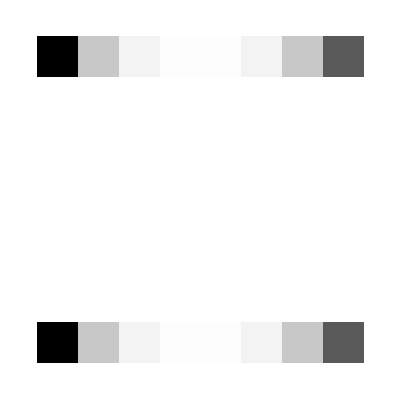
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[allome[[k]]],{k,1,11}]
```

```mathematica
Table[Sum[allome[[k]][[x,y]],{x,4,5},{y,4,5}],{k,1,11}]
```

{2.66522×10^-18,-2.08053×10^-7,-4.16105×10^-7,-6.24158×10^-7,-8.3221×10^-7,-1.04026×10^-6,-1.24832×10^-6,-1.45637×10^-6,-1.66442×10^-6,-1.87247×10^-6,-2.08053×10^-6}

## Check angular operator staggered

```mathematica
d0=staggeredDiracDNum[lat,0.0,torusBound];
oribitmtrR=oribitalStaggered[lat,1,torusBound];
spinmtrR=spinStaggered[lat,1,torusBound];
```

```mathematica
invd0=Inverse[d0];
```

```mathematica
ldldt=oribitmtrR.invd0.oribitmtrR.invd0;
ldsdt=oribitmtrR.invd0.spinmtrR.invd0;
sdldt=spinmtrR.invd0.oribitmtrR.invd0;
sdsdt=spinmtrR.invd0.spinmtrR.invd0;
```

```mathematica
Tr[ldsdt]
Tr[sdldt]
```

9.18747×10^-17

5.44009×10^-15

```mathematica
ldlddiagt=traceToXYZT[ldldt,lat];
ldsddiagt=traceToXYZT[ldsdt,lat];
sdlddiagt=traceToXYZT[sdldt,lat];
sdsddiagt=traceToXYZT[sdsdt,lat];
```

```mathematica
checkztsliceSame[ldlddiagt,lat]
checkztsliceSame[ldsddiagt,lat]
checkztsliceSame[sdlddiagt,lat]
checkztsliceSame[sdsddiagt,lat]
```

5.79436×10^-31

4.16053×10^-33

5.75964×10^-33

3.1885×10^-33

```mathematica
ztslice[ldlddiagt,1,1,lat]
ztslice[ldsddiagt,1,1,lat]
ztslice[sdlddiagt,1,1,lat]
ztslice[sdsddiagt,1,1,lat]
```

{{-0.0352279,-0.0386589,-0.0252995,-0.0184831,-0.0184831,-0.0252995,-0.0386589,-0.0352279},{-0.0386589,-0.0420898,-0.0287305,-0.0219141,-0.0219141,-0.0287305,-0.0420898,-0.0386589},{-0.0252995,-0.0287305,-0.0153711,-0.00855469,-0.00855469,-0.0153711,-0.0287305,-0.0252995},{-0.0184831,-0.0219141,-0.00855469,-0.00173828,-0.00173828,-0.00855469,-0.0219141,-0.0184831},{-0.0184831,-0.0219141,-0.00855469,-0.00173828,-0.00173828,-0.00855469,-0.0219141,-0.0184831},{-0.0252995,-0.0287305,-0.0153711,-0.00855469,-0.00855469,-0.0153711,-0.0287305,-0.0252995},{-0.0386589,-0.0420898,-0.0287305,-0.0219141,-0.0219141,-0.0287305,-0.0420898,-0.0386589},{-0.0352279,-0.0386589,-0.0252995,-0.0184831,-0.0184831,-0.0252995,-0.0386589,-0.0352279}}

{{-1.26716×10^-18,-9.55453×10^-19,1.97867×10^-18,-3.79471×10^-19,4.33681×10^-19,2.1684×10^-18,8.67362×10^-19,4.33681×10^-19},{2.95445×10^-18,-9.96111×10^-19,3.86247×10^-19,-7.86047×10^-19,-7.86047×10^-19,7.04731×10^-19,2.43945×10^-19,-1.54499×10^-18},{1.89058×10^-18,-9.62229×10^-19,-2.50722×10^-19,4.46386×10^-19,-2.60886×10^-19,3.65918×10^-19,-1.90159×10^-19,8.85996×10^-19},{-2.26327×10^-18,-1.20903×10^-18,1.11708×10^-19,1.57548×10^-19,-1.0842×10^-19,9.35757×10^-19,2.48809×10^-19,-2.31748×10^-18},{4.09964×10^-19,-4.7095×10^-19,-1.01644×10^-19,1.09267×10^-19,-3.01544×10^-19,-3.52366×10^-19,-1.7415×10^-18,-1.98883×10^-18},{4.06576×10^-20,-1.34509×10^-18,-6.87791×10^-19,-2.1684×10^-19,-2.03288×10^-20,-1.49078×10^-19,5.42101×10^-20,-1.02999×10^-18},{-8.13152×10^-19,-1.74828×10^-18,1.0571×10^-18,6.50521×10^-19,-4.33681×10^-19,1.51788×10^-18,4.33681×10^-19,2.1684×10^-19},{1.73472×10^-18,3.35751×10^-19,-1.84134×10^-18,2.81893×10^-18,-1.19262×10^-18,-2.75107×10^-19,-4.45842×10^-19,-2.60209×10^-18}}

{{0.00758898,0.00299479,0.00234375,0.00225043,0.00225043,0.00234375,0.00299479,0.00758898},{0.00299479,-0.00159939,-0.00225043,-0.00234375,-0.00234375,-0.00225043,-0.00159939,0.00299479},{0.00234375,-0.00225043,-0.00290148,-0.00299479,-0.00299479,-0.00290148,-0.00225043,0.00234375},{0.00225043,-0.00234375,-0.00299479,-0.00308811,-0.00308811,-0.00299479,-0.00234375,0.00225043},{0.00225043,-0.00234375,-0.00299479,-0.00308811,-0.00308811,-0.00299479,-0.00234375,0.00225043},{0.00234375,-0.00225043,-0.00290148,-0.00299479,-0.00299479,-0.00290148,-0.00225043,0.00234375},{0.00299479,-0.00159939,-0.00225043,-0.00234375,-0.00234375,-0.00225043,-0.00159939,0.00299479},{0.00758898,0.00299479,0.00234375,0.00225043,0.00225043,0.00234375,0.00299479,0.00758898}}

{{0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737},{0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737},{0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737},{0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737},{0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737},{0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737},{0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737},{0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737,0.00288737}}

```mathematica
ListPlot3D[ztslice[ldlddiagt,1,1,lat],PlotRange->All]
ListPlot3D[ztslice[ldsddiagt,1,1,lat],PlotRange->All]
ListPlot3D[ztslice[sdlddiagt,1,1,lat],PlotRange->All]
ListPlot3D[ztslice[sdsddiagt,1,1,lat],PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

## Check angular operator naive

```mathematica
lat={4,4,4,4};
```

```mathematica
d0naive=naiveD[lat,0.0,torusBound];
Inversed0naive=Inverse[d0naive];
spinnaive=spintermnaive[lat,1.0,torusBound];
orbitnaive=oribitalnaive[lat,1.0,torusBound];
```

```mathematica
traceToXYZTS[mtr_,L_]:=Block[{digmtr},
digmtr=Table[mtr[[n,n]],{n,1,Length[mtr]}];
Return[Table[digmtr[[4((x-1) L[[2]]L[[3]]L[[4]]+(y-1) L[[3]]L[[4]]+(z-1) L[[4]]+(t-1))+s]],{x,1,L[[1]]},{y,1,L[[2]]},{z,1,L[[3]]},{t,1,L[[4]]},{s,1,4}]]
];
ztsliceSpinor[digmtr_,z_,t_,s_,L_]:=Table[digmtr[[x,y,z,t,s]],{x,1,L[[1]]},{y,1,L[[2]]}];
checkztsliceSameSpinor[digmtr_,L_]:=Sum[If[z==1&&t==1&&s==1,0,checkDelta[ztsliceSpinor[digmtr,1,1,1,L],ztsliceSpinor[digmtr,z,t,s,L]]],{z,1,L[[3]]},{t,1,L[[4]]},{s,1,4}];
checkztsliceSameSpinorS[digmtr_,z_,t_,s_,L_]:=checkDelta[ztsliceSpinor[digmtr,1,1,1,L],ztsliceSpinor[digmtr,z,t,s,L]];
```

```mathematica
ldldnt=orbitnaive.Inversed0naive.orbitnaive.Inversed0naive;
ldsdnt=orbitnaive.Inversed0naive.spinnaive.Inversed0naive;
sdldnt=spinnaive.Inversed0naive.orbitnaive.Inversed0naive;
sdsdnt=spinnaive.Inversed0naive.spinnaive.Inversed0naive;
```

```mathematica
Tr[ldldnt]
Tr[ldsdnt]
Tr[sdldnt]
Tr[sdsdnt]
```

-5757.85+0. ⅈ

0.+0. ⅈ

0.+0. ⅈ

121.394+0. ⅈ

```mathematica
ldlddiagnt=traceToXYZTS[ldldnt,lat];
ldsddiagnt=traceToXYZTS[ldsdnt,lat];
sdlddiagnt=traceToXYZTS[sdldnt,lat];
sdsddiagnt=traceToXYZTS[sdsdnt,lat];
```

```mathematica
checkztsliceSameSpinor[ldlddiagnt,lat]
checkztsliceSameSpinor[ldsddiagnt,lat]
checkztsliceSameSpinor[sdlddiagnt,lat]
checkztsliceSameSpinor[sdsddiagnt,lat]
```

202.272

0.

0.

1.76954×10^-30

```mathematica
Print["z=1 vs 2,3,4"]
checkDelta[ztsliceSpinor[ldlddiagnt,1,1,1,lat],ztsliceSpinor[ldlddiagnt,2,1,1,lat]]
checkDelta[ztsliceSpinor[ldlddiagnt,1,1,1,lat],ztsliceSpinor[ldlddiagnt,3,1,1,lat]]
checkDelta[ztsliceSpinor[ldlddiagnt,1,1,1,lat],ztsliceSpinor[ldlddiagnt,4,1,1,lat]]
Print["t=1 vs 2,3,4"]
checkDelta[ztsliceSpinor[ldlddiagnt,1,1,1,lat],ztsliceSpinor[ldlddiagnt,1,2,1,lat]]
checkDelta[ztsliceSpinor[ldlddiagnt,1,1,1,lat],ztsliceSpinor[ldlddiagnt,1,3,1,lat]]
checkDelta[ztsliceSpinor[ldlddiagnt,1,1,1,lat],ztsliceSpinor[ldlddiagnt,1,4,1,lat]]
Print["s=1 vs 2,3,4"]
checkDelta[ztsliceSpinor[ldlddiagnt,1,1,1,lat],ztsliceSpinor[ldlddiagnt,1,1,2,lat]]
checkDelta[ztsliceSpinor[ldlddiagnt,1,1,1,lat],ztsliceSpinor[ldlddiagnt,1,1,3,lat]]
checkDelta[ztsliceSpinor[ldlddiagnt,1,1,1,lat],ztsliceSpinor[ldlddiagnt,1,1,4,lat]]
```

z=1 vs 2,3,4

1.13147

3.72623

7.7843

t=1 vs 2,3,4

3.43434×10^-29

1.80178×10^-28

2.37945×10^-28

s=1 vs 2,3,4

7.7843

1.16496×10^-29

7.7843

```mathematica
ztsliceSpinorAllZTS[digmtr_,L_]:=Table[Sum[digmtr[[x,y,z,t,s]],{z,1,L[[3]]},{t,1,L[[4]]},{s,1,4}],{x,1,L[[1]]},{y,1,L[[2]]}];
```

```mathematica
ldlddiagntxy=ztsliceSpinorAllZTS[ldlddiagnt,lat]
ldsddiagntxy=ztsliceSpinorAllZTS[ldsddiagnt,lat]
sdlddiagntxy=ztsliceSpinorAllZTS[sdlddiagnt,lat]
sdsddiagntxy=ztsliceSpinorAllZTS[sdsddiagnt,lat]
```

{{15.4064+0. ⅈ,4.46404+0. ⅈ,-12.7652+0. ⅈ,-36.2812+0. ⅈ},{-74.7799+0. ⅈ,-124.407+0. ⅈ,-130.026+0. ⅈ,-192.226+0. ⅈ},{-350.842+0. ⅈ,-451.088+0. ⅈ,-457.033+0. ⅈ,-569.853+0. ⅈ},{-705.364+0. ⅈ,-844.295+0. ⅈ,-838.629+0. ⅈ,-990.134+0. ⅈ}}

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

{{7.58712+0. ⅈ,7.58712+0. ⅈ,7.58712+0. ⅈ,7.58712+0. ⅈ},{7.58712+0. ⅈ,7.58712+0. ⅈ,7.58712+0. ⅈ,7.58712+0. ⅈ},{7.58712+0. ⅈ,7.58712+0. ⅈ,7.58712+0. ⅈ,7.58712+0. ⅈ},{7.58712+0. ⅈ,7.58712+0. ⅈ,7.58712+0. ⅈ,7.58712+0. ⅈ}}

```mathematica
ListPlot3D[ldlddiagntxy]
ListPlot3D[ldsddiagntxy]
ListPlot3D[sdlddiagntxy]
ListPlot3D[sdsddiagntxy]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

## Check angular operator naive projective plane

```mathematica
d0naivep=naiveD[lat,0.0,projectiveXY];
Inversed0naivep=Inverse[d0naivep];
spinnaivep=spintermnaive[lat,1.0,projectiveXY];
orbitnaivep=oribitalnaive[lat,1.0,projectiveXY];
```

```mathematica
ldldnp=orbitnaivep.Inversed0naivep.orbitnaivep.Inversed0naivep;
ldsdnp=orbitnaivep.Inversed0naivep.spinnaivep.Inversed0naivep;
sdldnp=spinnaivep.Inversed0naivep.orbitnaivep.Inversed0naivep;
sdsdnp=spinnaivep.Inversed0naivep.spinnaivep.Inversed0naivep;
```

```mathematica
Tr[ldldnp]
Tr[ldsdnp]
Tr[sdldnp]
Tr[sdsdnp]
```

-2826.12-3.08642×10^-14 ⅈ

-13.1621-5.55112×10^-16 ⅈ

-13.1621-4.11129×10^-16 ⅈ

120.735-2.185×10^-16 ⅈ

```mathematica
ldlddiagnp=traceToXYZTS[ldldnp,lat];
ldsddiagnp=traceToXYZTS[ldsdnp,lat];
sdlddiagnp=traceToXYZTS[sdldnp,lat];
sdsddiagnp=traceToXYZTS[sdsdnp,lat];
```

```mathematica
checkztsliceSameSpinor[ldlddiagnp,lat]
checkztsliceSameSpinor[ldsddiagnp,lat]
checkztsliceSameSpinor[sdlddiagnp,lat]
checkztsliceSameSpinor[sdsddiagnp,lat]
```

1428.98

1.40741

0.549403

2.61982×10^-30

```mathematica
ldlddiagnpxy=ztsliceSpinorAllZTS[ldlddiagnp,lat]
ldsddiagnpxy=ztsliceSpinorAllZTS[ldsddiagnp,lat]
sdlddiagnpxy=ztsliceSpinorAllZTS[sdlddiagnp,lat]
sdsddiagnpxy=ztsliceSpinorAllZTS[sdsddiagnp,lat]
```

{{-25.8703+8.32667×10^-16 ⅈ,15.5957-6.93889×10^-16 ⅈ,-11.3531-1.52656×10^-15 ⅈ,2.1863+1.38778×10^-16 ⅈ},{33.2315+1.05471×10^-15 ⅈ,-88.0942-1.55431×10^-15 ⅈ,-118.282-3.747×10^-16 ⅈ,-29.594+2.77556×10^-16 ⅈ},{-78.5646-1.52656×10^-16 ⅈ,-391.384+3.03924×10^-15 ⅈ,-454.785-1.80411×10^-16 ⅈ,-293.694-1.88738×10^-15 ⅈ},{-319.754+5.21111×10^-15 ⅈ,-223.243+1.11022×10^-16 ⅈ,-209.478+6.66134×10^-16 ⅈ,-633.042-3.57492×10^-14 ⅈ}}

{{-0.297115+4.33681×10^-19 ⅈ,-0.0990382+1.97325×10^-17 ⅈ,0.0990382+5.25838×10^-18 ⅈ,0.297115-4.98733×10^-18 ⅈ},{0.599149+5.07407×10^-17 ⅈ,0.760024-8.1532×10^-17 ⅈ,0.977174+1.73472×10^-18 ⅈ,1.31813+9.02056×10^-17 ⅈ},{-1.55779+1.38778×10^-17 ⅈ,-1.62862-1.56125×10^-16 ⅈ,-1.84577-1.59595×10^-16 ⅈ,-2.27677+4.85723×10^-17 ⅈ},{-2.0798-3.81639×10^-17 ⅈ,-2.27788-2.08167×10^-17 ⅈ,-2.47596-7.63278×10^-17 ⅈ,-2.67403-2.498×10^-16 ⅈ}}

{{0.124965-8.50015×10^-17 ⅈ,0.683594-6.93889×10^-18 ⅈ,1.92978+3.98986×10^-17 ⅈ,0.278759-5.24754×10^-17 ⅈ},{3.28104+9.02056×10^-17 ⅈ,4.1265-1.249×10^-16 ⅈ,4.77715-1.5786×10^-16 ⅈ,3.43483-9.97466×10^-18 ⅈ},{-6.90239-9.62772×10^-17 ⅈ,-0.361355-3.81639×10^-17 ⅈ,-1.01201-6.93889×10^-18 ⅈ,-7.05618-1.00614×10^-16 ⅈ},{-5.27429-7.71952×10^-17 ⅈ,-2.25912+1.04083×10^-17 ⅈ,-3.50531+9.36751×10^-17 ⅈ,-5.42809+1.09288×10^-16 ⅈ}}

{{7.90427-8.5923×10^-18 ⅈ,7.7933-5.71103×10^-17 ⅈ,7.7933-4.3097×10^-17 ⅈ,7.90427-3.77302×10^-17 ⅈ},{7.7933-4.19586×10^-17 ⅈ,6.69281-8.07731×10^-18 ⅈ,6.69281+2.08709×10^-18 ⅈ,7.7933-4.41135×10^-18 ⅈ},{7.7933-3.04661×10^-17 ⅈ,6.69281+2.0261×10^-18 ⅈ,6.69281+4.04882×10^-18 ⅈ,7.7933+3.3285×10^-17 ⅈ},{7.90427-2.95445×10^-17 ⅈ,7.7933-9.1073×10^-18 ⅈ,7.7933+2.90566×10^-17 ⅈ,7.90427-1.89082×10^-17 ⅈ}}

```mathematica
ListPlot3D[ldlddiagnpxy]
ListPlot3D[ldsddiagnpxy]
ListPlot3D[sdlddiagnpxy]
ListPlot3D[sdsddiagnpxy]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
ListPlot3D[ldlddiagnpxy+ldsddiagnpxy]
ListPlot3D[sdlddiagnpxy+sdsddiagnpxy]
```

-Graphics3D-

-Graphics3D-

## Wilson Dirac fermion

## Some results

```mathematica
xx={x1,x2,x3};
yy={y1,y2,y3};
Table[xx[[x]]yy[[y]],{x,1,3},{y,1,3}]
```

(x1 y1 | x1 y2 | x1 y3
x2 y1 | x2 y2 | x2 y3
x3 y1 | x3 y2 | x3 y3)

```mathematica
(* x=2,y=3 *)
{{0,1,0}}.Table[xx[[x]]yy[[y]],{x,1,3},{y,1,3}].{{0},{0},{1}}
```

(x2 y3)

```mathematica
sigma12=I/2(gm1.gm2-gm2.gm1);
sigma13=I/2(gm1.gm3-gm3.gm1);
sigma14=I/2(gm1.gm4-gm4.gm1);
sigma23=I/2(gm2.gm3-gm3.gm2);
sigma24=I/2(gm2.gm4-gm4.gm2);
sigma34=I/2(gm3.gm4-gm4.gm3);
```

```mathematica
sigma12.sigma12
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MatrixExp[I 0.3 sigma12]
```

(0.955336-0.29552 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.955336+0.29552 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.955336-0.29552 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.955336+0.29552 ⅈ)

```mathematica
Cos[0.3]gmu+Sin[0.3]sigma12 I
```

(0.955336-0.29552 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.955336+0.29552 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.955336-0.29552 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.955336+0.29552 ⅈ)

```mathematica
MatrixExp[I 0.3 gm1]
```

(0.955336+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.29552+0. ⅈ
0.+0. ⅈ | 0.955336+0. ⅈ | 0.29552+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -0.29552+0. ⅈ | 0.955336+0. ⅈ | 0.+0. ⅈ
-0.29552+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.955336+0. ⅈ)

```mathematica
Cos[0.3]gmu+Sin[0.3]gm1 I
```

(0.955336+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.29552+0. ⅈ
0.+0. ⅈ | 0.955336+0. ⅈ | 0.29552+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -0.29552+0. ⅈ | 0.955336+0. ⅈ | 0.+0. ⅈ
-0.29552+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.955336+0. ⅈ)

```mathematica
gm51=gm5.gm1;
```

```mathematica
MatrixExp[0.3 gm51]
```

(0.955336+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.-0.29552 ⅈ
0.+0. ⅈ | 0.955336+0. ⅈ | 0.-0.29552 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.-0.29552 ⅈ | 0.955336+0. ⅈ | 0.+0. ⅈ
0.-0.29552 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.955336+0. ⅈ)

```mathematica
Cos[0.3]gmu+Sin[0.3]gm51
```

(0.955336 | 0. | 0. | 0.-0.29552 ⅈ
0. | 0.955336 | 0.-0.29552 ⅈ | 0.
0. | 0.-0.29552 ⅈ | 0.955336 | 0.
0.-0.29552 ⅈ | 0. | 0. | 0.955336)

```mathematica
gm4.sigma12-sigma12.gm4
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
I gm4.sigma12
```

(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0)

```mathematica
gm5.gm3
```

(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0)

```mathematica
I gm5.gm4.gm1.gm5-ConjugateTranspose[I gm4.gm1]
I gm5.gm4.gm2.gm5-ConjugateTranspose[I gm4.gm2]
I gm5.gm4.gm3.gm5-ConjugateTranspose[I gm4.gm3]
gm5.gm4.gm4.gm5-ConjugateTranspose[gm4.gm4]
gm5.gm4.gm5.gm5-ConjugateTranspose[gm4.gm5]
I gm5.gm4.sigma12.gm5-ConjugateTranspose[I gm4.sigma12]
I gm5.gm4.sigma13.gm5-ConjugateTranspose[I gm4.sigma13]
gm5.gm4.sigma14.gm5-ConjugateTranspose[gm4.sigma14]
I gm5.gm4.sigma23.gm5-ConjugateTranspose[I gm4.sigma23]
gm5.gm4.sigma24.gm5-ConjugateTranspose[gm4.sigma24]
gm5.gm4.sigma34.gm5-ConjugateTranspose[gm4.sigma34]
I gm5.gm4.gm5.gm1.gm5-ConjugateTranspose[I gm4.gm5.gm1]
I gm5.gm4.gm5.gm2.gm5-ConjugateTranspose[I gm4.gm5.gm2]
I gm5.gm4.gm5.gm3.gm5-ConjugateTranspose[I gm4.gm5.gm3]
gm5.gm4.gm5.gm4.gm5-ConjugateTranspose[gm4.gm5.gm4]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

«12 more identical outputs»

```mathematica
I gm5.gm1.gm5-ConjugateTranspose[I gm1]
I gm5.gm2.gm5-ConjugateTranspose[I gm2]
I gm5.gm3.gm5-ConjugateTranspose[I gm3]
I gm5.gm4.gm5-ConjugateTranspose[I gm4]
gm5.gm5.gm5-ConjugateTranspose[gm5]
gm5.sigma12.gm5-ConjugateTranspose[sigma12]
gm5.sigma13.gm5-ConjugateTranspose[sigma13]
gm5.sigma14.gm5-ConjugateTranspose[sigma14]
gm5.sigma23.gm5-ConjugateTranspose[sigma23]
gm5.sigma24.gm5-ConjugateTranspose[sigma24]
gm5.sigma34.gm5-ConjugateTranspose[sigma34]
gm5.gm5.gm1.gm5-ConjugateTranspose[gm5.gm1]
gm5.gm5.gm2.gm5-ConjugateTranspose[gm5.gm2]
gm5.gm5.gm3.gm5-ConjugateTranspose[gm5.gm3]
gm5.gm5.gm4.gm5-ConjugateTranspose[gm5.gm4]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

«12 more identical outputs»

```mathematica
-I gm4.{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}}
```

(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0)